```mathematica
ClearAll["Global`*"];
```

```mathematica
df = 21;
td=StudentTDistribution[df];
N[Kurtosis[td],21]
N[Mean[td],21]
N[Skewness[td],21]
N[Variance[td],21]
```

3.35294117647058823529

0

0

1.10526315789473684211

```mathematica
lambda=3;
df=21;
ntd=NoncentralStudentTDistribution[df,lambda];
N[Mean[ntd],21]
N[Variance[ntd],21]
N[Skewness[ntd],21]
N[Kurtosis[ntd],21]
```

3.11273629794486754698

1.3635043184038491925

0.430814083288819887296

3.61902917492752013195

```mathematica
nd=NormalDistribution[3,1/2];
N[Kurtosis[nd],21]
N[Mean[nd],21]
N[Skewness[nd],21]
N[Variance[nd],21]
```

3.

3.

0

0.25

```mathematica
df1=4;
df2=9;
fd=FRatioDistribution[df1,df2];
N[Mean[fd],21]
N[Variance[fd],21]
N[Skewness[fd],21]
N[Kurtosis[fd],21]
```

1.28571428571428571429

1.8183673469387755102

4.76731294622796157723

117.272727272727272727

```mathematica
m=3;
s=1/2;
lnd=LogNormalDistribution[m,s];
N[Mean[lnd],21]
N[Variance[lnd],21]
N[Skewness[lnd],21]
N[Kurtosis[lnd],21]
```

22.7598950935267279834

147.128808376019814754

1.75018965506971818265

8.898445673784779013

```mathematica
shapeA=2;
shapeB=25/10;
bd = BetaDistribution[shapeA,shapeB];
N[Mean[bd],21]
N[Variance[bd],21]
N[Skewness[bd],21]
N[Kurtosis[bd],21]
```

0.444444444444444444444

0.0448933782267115600449

0.161355207410792545691

2.23384615384615384615

```mathematica
loc=99;
scale=25/100;
cd=CauchyDistribution[loc,scale];
N[Mean[cd],21]
N[Variance[cd],21]
N[Skewness[cd],21]
N[Kurtosis[cd],21]
```

Indeterminate

Indeterminate

Indeterminate

«1 more identical outputs»

```mathematica
loc=0;
scale=1;
cd=LaplaceDistribution[loc,scale];
N[CDF[cd,1],7]
N[CDF[cd,-8],7]
N[CDF[cd,19],7]
N[CDF[cd,1/2],7]
```

0.8160603

0.0001677313

1.

0.6967347

```mathematica
loc=0;
scale=1;
cd=LaplaceDistribution[loc,scale];
N[PDF[cd,1],7]
N[PDF[cd,-8],7]
N[PDF[cd,19],7]
N[PDF[cd,1/2],7]
```

0.1839397

0.0001677313

2.801398×10^-9

0.3032653

```mathematica
loc=0;
scale=1;
cd=LaplaceDistribution[loc,scale];
N[InverseCDF[cd,1],7]
N[InverseCDF[cd,1/2],7]
N[InverseCDF[cd,75/100],7]
N[InverseCDF[cd,99/100],7]
N[InverseCDF[cd,0],7]
```

∞

0

0.6931472

3.912023

-∞

```mathematica
loc=0;
scale=1;
cd=LaplaceDistribution[loc,scale];
N[Mean[cd],21]
N[Variance[cd],21]
N[Skewness[cd],21]
N[Kurtosis[cd],21]
```

0

2.

0

6.

```mathematica
loc=3;
scale=2;
d=LogisticDistribution[loc,scale];
N[Mean[d],21]
N[Variance[d],21]
N[Skewness[d],21]
N[Kurtosis[d],21]
```

3.

13.1594725347858114918

0

4.2

```mathematica
min=1;
shape=22;
pd=ParetoDistribution[min, shape];
```

```mathematica
N[CDF[pd,3/2],7]
```

0.9998663

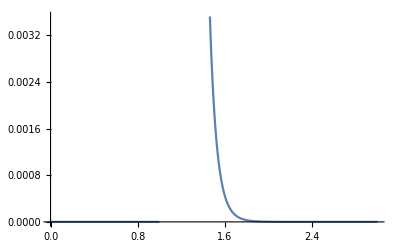

```mathematica
Plot[PDF[pd,x],{x,0,3}]
```

```mathematica
min=1;
shape=22;
pd=ParetoDistribution[min, shape];
N[InverseCDF[pd,0],21]
N[InverseCDF[pd, 25/100],21]
N[InverseCDF[pd,5/10],21]
N[InverseCDF[pd,75/100],21]
N[InverseCDF[pd,99/100],21]
N[InverseCDF[pd,1],21]
```

1.

1.0131623286004264924

1.03200827973420963159

1.06504108943996267819

1.23284673944206613905

∞

```mathematica
min=1;
shape=22;
pd=ParetoDistribution[min,shape];
N[PDF[pd,0],21]
N[PDF[pd,1],21]
N[PDF[pd,1001/1000],21]
N[PDF[pd,1050/1000],21]
N[PDF[pd,1850/1000],21]
N[PDF[pd,2],21]
N[PDF[pd,25/10],21]
```

0

22.

21.5000217271321940712

7.16256872752922185937

0.0000157569779601844505236

2.6226043701171875×10^-6

1.548112371908608×10^-8

```mathematica
min=1;
shape=22;
pd=ParetoDistribution[min,shape];
N[InverseCDF[pd,0],21]
N[InverseCDF[pd,25/100],21]
N[InverseCDF[pd,5/10],21]
N[InverseCDF[pd,75/100],21]
N[InverseCDF[pd,99/100],21]
N[InverseCDF[pd,1],21]
```

1.

1.0131623286004264924

1.03200827973420963159

1.06504108943996267819

1.23284673944206613905

∞

```mathematica
N[Mean[pd],21]
N[Variance[pd],21]
N[Skewness[pd],21]
N[Kurtosis[pd],21]
```

1.04761904761904761905

0.00249433106575963718821

2.3083831108051182374

11.7703349282296650718

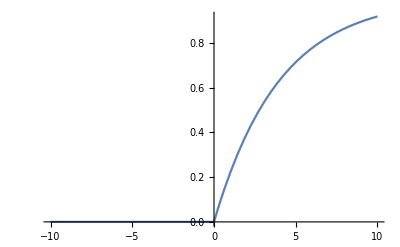

```mathematica
lambda=1/4;
ed=ExponentialDistribution[lambda];
Plot[CDF[ed,x],{x,-10,10}]
```

```mathematica
N[InverseCDF[ed,0],21]
N[InverseCDF[ed,25/100],21]
N[InverseCDF[ed,5/10],21]
N[InverseCDF[ed,75/100],21]
N[InverseCDF[ed,99/100],21]
N[InverseCDF[ed,1],21]
```

0

1.15072828980712370976

2.77258872223978123767

5.54517744447956247534

18.4206807439523654721

∞

```mathematica
N[Mean[ed],21]
N[Variance[ed],21]
N[Skewness[ed],21]
N[Kurtosis[ed],21]
```

4.

16.

2.

9.

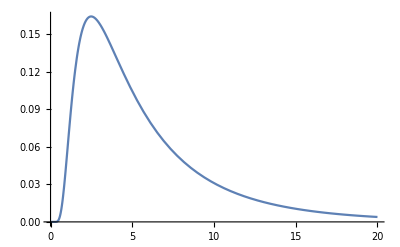

```mathematica
mu=6;
lambda=9;
wd=InverseGaussianDistribution[mu,lambda];
Plot[PDF[wd,x],{x,0,20}]
```

```mathematica
N[CDF[wd,0],21]
N[CDF[wd,1],21]
N[CDF[wd,2],21]
N[CDF[wd,3],21]
N[CDF[wd,10],21]
N[CDF[wd,33],21]
N[CDF[wd,145],21]
```

0

0.010882145282151315487

0.125627012864498276906

0.287386744404773626164

0.851063810667129652088

0.997518962516710678217

0.999999999702767058076

```mathematica
N[PDF[wd,0],21]
N[PDF[wd,1],21]
N[PDF[wd,2],21]
N[PDF[wd,3],21]
N[PDF[wd,10],21]
N[PDF[wd,33],21]
N[PDF[wd,145],21]
```

0

0.0525849014807056120865

0.155665311532723013753

0.158302949877769673488

0.0309864928480366992183

0.000399039071184676275858

4.00272220943724302952×10^-11

```mathematica
N[InverseCDF[wd,0],21]
N[InverseCDF[wd,25/100],21]
N[InverseCDF[wd,5/10],21]
N[InverseCDF[wd,75/100],21]
N[InverseCDF[wd,99/100],21]
N[InverseCDF[wd,999/1000],21]
N[InverseCDF[wd,1],21]
```

0

2.76686873332207861117

4.53675199081610130561

7.57917596871024542035

24.5614684372629823155

38.7320805901883006582

∞

```mathematica
N[Mean[wd],21]
N[Variance[wd],21]
N[Skewness[wd],21]
N[Kurtosis[wd],21]
```

6.

24.

2.4494897427831780982

13.

```mathematica
shape=2;
scale=3;
d=GammaDistribution[shape,scale];
Plot[PDF[wd,x],{x,0,20}]
```

-Graphics-

```mathematica
N[CDF[d,0],21]
N[CDF[d,1],21]
N[CDF[d,2],21]
N[CDF[d,3],21]
N[CDF[d,10],21]
N[CDF[d,33],21]
N[CDF[d,145],21]
```

0

0.0446249192349476660992

0.14430480161234662188

0.264241117657115356809

0.845412695495239610381

0.999799579590517052088

0.99999999999999999995

```mathematica
N[PDF[d,0],21]
N[PDF[d,1],21]
N[PDF[d,2],21]
N[PDF[d,3],21]
N[PDF[d,10],21]
N[PDF[d,33],21]
N[PDF[d,145],21]
```

0

0.0796145900637543611584

0.114092693118353783749

0.122626480390480773865

0.0396377703858359973383

0.0000612395695642340841463

1.64522588620458773×10^-20

```mathematica
N[InverseCDF[d,0],21]
N[InverseCDF[d,25/100],21]
N[InverseCDF[d,5/10],21]
N[InverseCDF[d,75/100],21]
N[InverseCDF[d,99/100],21]
N[InverseCDF[d,999/1000],21]
N[InverseCDF[d,1],21]
```

0

2.88383628934433128754

5.03504097004998196024

8.07790358666908731226

19.9150562039814368081

27.7002404293547571913

∞

```mathematica
N[Mean[d],21]
N[Variance[d],21]
N[Skewness[d],21]
N[Kurtosis[d],21]
```

6.

18.

1.4142135623730950488

6.

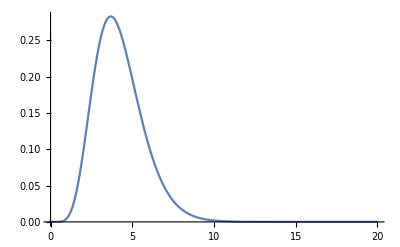

```mathematica
shape=8;
scale=19/10;
d=ErlangDistribution[shape,scale];
Plot[PDF[d,x],{x,0,20}]
```

```mathematica
N[CDF[d,-1],21]
N[CDF[d,1],21]
N[CDF[d,2],21]
N[CDF[d,22/10],21]
N[CDF[d,45/10],21]
N[CDF[d,7],21]
N[CDF[d,10],21]
```

0

0.000793457613267557042372

0.0401073776861547292702

0.0625806276334696425021

0.620845136890394243952

0.953851071263071931215

0.998486657386375206401

```mathematica
N[PDF[d,-1],21]
N[PDF[d,1],21]
N[PDF[d,2],21]
N[PDF[d,22/10],21]
N[PDF[d,45/10],21]
N[PDF[d,7],21]
N[PDF[d,10],21]
```

0

0.00504009538397410085449

0.0964915337384170109056

0.128589676154648556029

0.243707024534075753055

0.0464694938322868155464

0.00188800489092865877089

```mathematica
N[InverseCDF[d,0],21]
N[InverseCDF[d,25/100],21]
N[InverseCDF[d,5/10],21]
N[InverseCDF[d,75/100],21]
N[InverseCDF[d,99/100],21]
N[InverseCDF[d,999/1000],21]
N[InverseCDF[d,1],21]
```

0

3.13479465721473572797

4.03644707500042310756

5.09706847910118785655

8.42103339705662662358

10.3295670502022305302

∞

```mathematica
N[Mean[d],21]
N[Variance[d],21]
N[Skewness[d],21]
N[Kurtosis[d],21]
```

4.21052631578947368421

2.2160664819944598338

0.707106781186547524401

3.75

```mathematica
ClearAll["Global`*"];
```

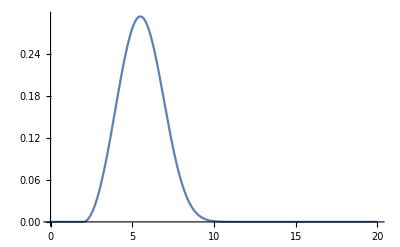

```mathematica
shape=3;
scale=4;
loc=2;
d=WeibullDistribution[shape,scale,loc];
Plot[PDF[d,x],{x,0,20}]
```

```mathematica
N[CDF[d,-1],21]
N[CDF[d,29/10],21]
N[CDF[d,3],21]
N[CDF[d,31/10],21]
N[CDF[d,45/10],21]
N[CDF[d,7],21]
N[CDF[d,22],21]
```

0

0.0113259974465415820934

0.015503562994591594013

0.0205821113758218963048

0.216622535939181796504

0.858169840912657470462

1.

```mathematica
N[PDF[d,-1],21]
N[PDF[d,29/10],21]
N[PDF[d,3],21]
N[PDF[d,31/10],21]
N[PDF[d,45/10],21]
N[PDF[d,7],21]
N[PDF[d,22],21]
```

0

0.0375387160344516243049

0.0461482704846285190306

0.055551358370402601819

0.229505116424067833055

0.166207217680479526802

9.68703868657098933797×10^-54

```mathematica
N[InverseCDF[d,0],21]
N[InverseCDF[d,25/100],21]
N[InverseCDF[d,5/10],21]
N[InverseCDF[d,75/100],21]
N[InverseCDF[d,99/100],21]
N[InverseCDF[d,999/1000],21]
N[InverseCDF[d,1],21]
```

2.

4.64056942859838095934

5.53998817800207087498

6.46010562184380828507

8.65490539680019769957

9.61796499056221876841

∞

```mathematica
N[Mean[d],21]
N[Variance[d],21]
N[Skewness[d],21]
N[Kurtosis[d],21]
```

5.57191804627699684487

1.68532615789565960689

0.16810284222940108243

2.7294636330961206701

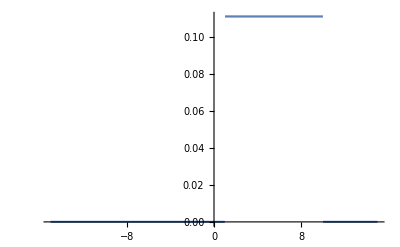

```mathematica
ClearAll["Global`*"];
min=1;
max=10;
d=UniformDistribution[{min,max}];
Plot[PDF[d,x],{x,-15,15}]
```

```mathematica
N[CDF[d,0],21]
N[CDF[d,29/10],21]
N[CDF[d,3],21]
N[CDF[d,31/10],21]
N[CDF[d,45/10],21]
N[CDF[d,7],21]
N[CDF[d,22],21]
```

0

0.211111111111111111111

0.222222222222222222222

0.233333333333333333333

0.388888888888888888889

0.666666666666666666667

1.

```mathematica
N[PDF[d,0],21]
N[PDF[d,29/10],21]
N[PDF[d,3],21]
N[PDF[d,31/10],21]
N[PDF[d,45/10],21]
N[PDF[d,7],21]
N[PDF[d,22],21]
```

0

0.111111111111111111111

0.111111111111111111111

0.111111111111111111111

«2 more identical outputs»

0

```mathematica
N[InverseCDF[d,0],21]
N[InverseCDF[d,25/100],21]
N[InverseCDF[d,5/10],21]
N[InverseCDF[d,75/100],21]
N[InverseCDF[d,99/100],21]
N[InverseCDF[d,999/1000],21]
N[InverseCDF[d,1],21]
```

1.

3.25

5.5

7.75

9.91

9.991

10.

```mathematica
N[Mean[d],21]
N[Variance[d],21]
N[Skewness[d],21]
N[Kurtosis[d],21]
```

5.5

6.75

0

1.8

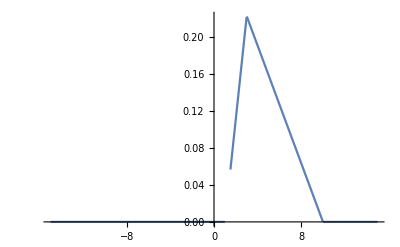

```mathematica
ClearAll["Global`*"];
min=1;
max=10;
mode=3;
d=TriangularDistribution[{min,max},mode];
Plot[PDF[d,x],{x,-15,15}]
```

```mathematica
N[CDF[d,0],21]
N[CDF[d,29/10],21]
N[CDF[d,3],21]
N[CDF[d,31/10],21]
N[CDF[d,45/10],21]
N[CDF[d,7],21]
N[CDF[d,22],21]
```

0

0.200555555555555555556

0.222222222222222222222

0.244285714285714285714

0.51984126984126984127

0.857142857142857142857

1.

```mathematica
N[PDF[d,0],21]
N[PDF[d,29/10],21]
N[PDF[d,3],21]
N[PDF[d,31/10],21]
N[PDF[d,45/10],21]
N[PDF[d,7],21]
N[PDF[d,22],21]
```

0

0.211111111111111111111

0.222222222222222222222

0.219047619047619047619

0.174603174603174603175

0.0952380952380952380952

0

```mathematica
N[InverseCDF[d,0],21]
N[InverseCDF[d,25/100],21]
N[InverseCDF[d,5/10],21]
N[InverseCDF[d,75/100],21]
N[InverseCDF[d,99/100],21]
N[InverseCDF[d,999/1000],21]
N[InverseCDF[d,1],21]
```

1.

3.12613645756623999012

4.38751391983908792162

6.03137303340311411425

9.20627460668062282285

9.74900199203977733561

10.

```mathematica
N[Mean[d],21]
N[Variance[d],21]
N[Skewness[d],21]
N[Kurtosis[d],21]
```

4.66666666666666666667

3.72222222222222222222

0.453853262394983221953

2.4

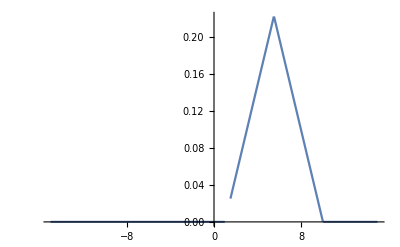

```mathematica
ClearAll["Global`*"];
min=1;
max=10;
d=TriangularDistribution[{min,max}];
Plot[PDF[d,x],{x,-15,15}]
```

```mathematica
N[CDF[d,0],21]
N[CDF[d,29/10],21]
N[CDF[d,3],21]
N[CDF[d,31/10],21]
N[CDF[d,45/10],21]
N[CDF[d,7],21]
N[CDF[d,22],21]
```

0

0.0891358024691358024691

0.0987654320987654320988

0.108888888888888888889

0.302469135802469135802

0.777777777777777777778

1.

```mathematica
N[PDF[d,0],21]
N[PDF[d,29/10],21]
N[PDF[d,3],21]
N[PDF[d,31/10],21]
N[PDF[d,45/10],21]
N[PDF[d,7],21]
N[PDF[d,22],21]
```

0

0.0938271604938271604938

0.0987654320987654320988

0.103703703703703703704

0.172839506172839506173

0.148148148148148148148

0

```mathematica
N[InverseCDF[d,0],21]
N[InverseCDF[d,25/100],21]
N[InverseCDF[d,5/10],21]
N[InverseCDF[d,75/100],21]
N[InverseCDF[d,99/100],21]
N[InverseCDF[d,999/1000],21]
N[InverseCDF[d,1],21]
```

1.

4.1819805153394638598

5.5

6.8180194846605361402

9.36360389693210722804

9.79875388202501892732

10.

```mathematica
N[Mean[d],21]
N[Variance[d],21]
N[Skewness[d],21]
N[Kurtosis[d],21]
```

5.5

3.375

0

2.4

```mathematica
ClearAll["Global`*"];
```

```mathematica
lambda=1;
d=PoissonDistribution[lambda];
```

```mathematica
N[PDF[d,0],21]
N[PDF[d,1],21]
N[PDF[d,2],21]
N[PDF[d,3],21]
N[PDF[d,4],21]
N[PDF[d,5],21]
N[PDF[d,6],21]
N[PDF[d,7],21]
N[PDF[d,8],21]
N[PDF[d,9],21]
```

0.367879441171442321596

0.367879441171442321596

0.183939720585721160798

0.0613132401952403869326

0.0153283100488100967331

0.00306566200976201934663

0.000510943668293669891105

0.000072991952613381413015

9.12399407667267662687×10^-6

1.01377711963029740299×10^-6

```mathematica
N[CDF[d,0],21]
N[CDF[d,1],21]
N[CDF[d,2],21]
N[CDF[d,3],21]
N[CDF[d,4],21]
N[CDF[d,5],21]
N[CDF[d,6],21]
N[CDF[d,7],21]
N[CDF[d,8],21]
N[CDF[d,9],21]
```

0.367879441171442321596

0.735758882342884643191

0.919698602928605803989

0.981011843123846190921

0.996340153172656287655

0.999405815182418307001

0.999916758850711976892

0.999989750803325358305

0.999998874797402030982

0.999999888574521661279

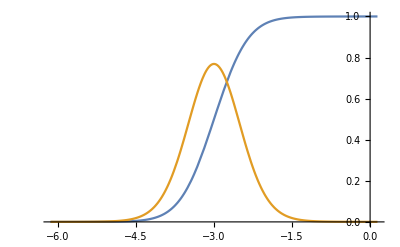

```mathematica
ClearAll["Global`*"];
a=-3;
b=4;
d=VonMisesDistribution[a,b];
Plot[{CDF[d,x],PDF[d,x]},{x,a-Pi,a+Pi}]
```

```mathematica
N[CDF[d,a-Pi-1],21]
N[CDF[d,-Pi-1],21]
N[CDF[d,-25/10],21]
N[CDF[d,-20/100],21]
N[CDF[d,-44/10],21]
N[CDF[d,0-Pi/2],21]
N[CDF[d,0],21]
N[CDF[d,a+Pi+1],21]
```

0

0.019538702136798554602

0.829488464005985508796

0.999904581125379364584

0.00722697637072942637724

0.993539629762563788614

0.999962986474166847826

1.

```mathematica
N[PDF[d,a-Pi-1],21]
N[PDF[d,-Pi-1],21]
N[PDF[d,-25/10],21]
N[PDF[d,-20/100],21]
N[PDF[d,-44/10],21]
N[PDF[d,0-Pi/2],21]
N[PDF[d,0],21]
N[PDF[d,a+Pi+1],21]
```

0

0.0744027395631070328565

0.471177869330735027666

0.000324982499557601827956

0.0277927164636370027697

0.0247638628979559132417

0.000268456988587833058582

0

```mathematica
N[InverseCDF[d,0],21]
N[InverseCDF[d,25/100],21]
N[InverseCDF[d,5/10],21]
N[InverseCDF[d,75/100],21]
N[InverseCDF[d,99/100],21]
N[InverseCDF[d,999/1000],21]
N[InverseCDF[d,1],21]
```

-6.14159265358979323846

-3.3520552735719090448

-3.

-2.64794472642809095508

-1.68421199711729556367

-1.04475697892580395363

0.141592653589793238463

```mathematica
N[Mean[d],21]
N[Variance[d],21]
N[Skewness[d],21]
N[Kurtosis[d],21]
```

-3.

0.298228377673744754555

0

3.6885501189965312939

```mathematica
V=1-BesselI[1,b]/BesselI[0,b]
```

1-BesselI[1,4]/BesselI[0,4]

```mathematica
N[V,21]
```

0.136477388975449417145

```mathematica
ClearAll["Global`*"];
PDF[RayleighDistribution[s]]
CDF[RayleighDistribution[s]]
InverseCDF[RayleighDistribution[s],p]
Mean[RayleighDistribution[s]]
Variance[RayleighDistribution[s]]
Skewness[RayleighDistribution[s]]
Kurtosis[RayleighDistribution[s]]
```

Function[x,Piecewise[{{(x ⅇ^(-x^2/(2 s^2)))/s^2, x>0}, {0, True}}],Listable]

Function[x,Piecewise[{{1-ⅇ^(-x^2/(2 s^2)), x>0}, {0, True}}],Listable]

s √(-Log[(1-p)^2])

√(π/2) s

(2-π/2) s^2

((-3+π) √(π/2))/(2-π/2)^(3/2)

(32-3 π^2)/(4-π)^2

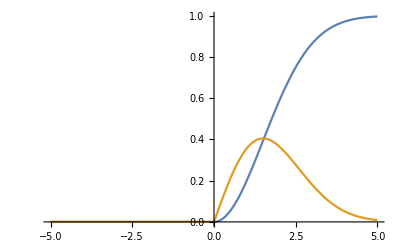

```mathematica
ClearAll["Global`*"];
s=3/2;
d=RayleighDistribution[s];
Plot[{CDF[d,x],PDF[d,x]},{x,-5,5}]
```

```mathematica
N[PDF[d,-1],21]
N[PDF[d,0],21]
N[PDF[d,1/100],21]
N[PDF[d,1],21]
N[PDF[d,11/10],21]
N[PDF[d,3],21]
N[PDF[d,10],21]
```

0

0

0.0044443456801097312402

0.355883290185248018124

0.373622658528284221473

0.180447044315483589192

9.92725082756961935157×10^-10

```mathematica
N[CDF[d,-1],21]
N[CDF[d,0],21]
N[CDF[d,1/100],21]
N[CDF[d,1],21]
N[CDF[d,11/10],21]
N[CDF[d,3],21]
N[CDF[d,10],21]
```

0

0

0.0000222219753104709546309

0.199262597083191959222

0.235771834828509546987

0.864664716763387308106

0.99999999977663685638

```mathematica
N[InverseCDF[d,25/100],21]
N[InverseCDF[d,5/10],21]
N[InverseCDF[d,75/100],21]
N[InverseCDF[d,99/100],21]
N[InverseCDF[d,999/1000],21]
N[InverseCDF[d,1],21]
```

1.13779142466139819887

1.76611503377321203652

2.49766383347309326906

4.55228138815543905259

5.57538328327475767043

∞

```mathematica
ClearAll["Global`*"];
ClearAll["Global`*"];
PDF[ExtremeValueDistribution[a,b],x]
CDF[ExtremeValueDistribution[a,b],x]
InverseCDF[ExtremeValueDistribution[a,b],p]
Mean[ExtremeValueDistribution[a,b]]
Variance[ExtremeValueDistribution[a,b]]
Skewness[ExtremeValueDistribution[a,b]]
Kurtosis[ExtremeValueDistribution[a,b]]
a=-2;
b=1;
d=ExtremeValueDistribution[a,b];
Plot[{CDF[d,x],PDF[d,x]},{x,-5,5}]
```

(ⅇ^(-ⅇ^((a-x)/b)+(a-x)/b))/b

ⅇ^(-ⅇ^(-(-a+x)/b))

ConditionalExpression[Piecewise[{{a-b Log[-Log[p]], 0<p<1}, {-∞, p≤0}, {∞, True}}],0≤p≤1]

a+b EulerGamma

(b^2 π^2)/6

(12 √6 Zeta[3])/π^3

27/5

```mathematica
N[PDF[d,-6],21]
N[PDF[d,-5],21]
N[PDF[d,-4/100],21]
N[PDF[d,-2],21]
N[PDF[d,-11/100],21]
N[PDF[d,0],21]
N[PDF[d,2],21]
N[PDF[d,5],21]
```

1.06048039970427672992×10^-22

3.80054250404435771071×10^-8

0.122351354198388769973

0.367879441171442321596

0.129889419617261299978

0.118204951593143145999

0.0179832296967136435659

0.000911050815848220300461

```mathematica
N[CDF[d,-6],21]
N[CDF[d,-5],21]
N[CDF[d,-4/100],21]
N[CDF[d,-2],21]
N[CDF[d,-11/100],21]
N[CDF[d,0],21]
N[CDF[d,2],21]
N[CDF[d,5],21]
```

1.94233760495640183858×10^-24

1.89217869483829263358×10^-9

0.868612280319186993522

0.367879441171442321596

0.859785956213361748121

0.873423018493116642989

0.98185107306166648292

0.999088533672457833191

```mathematica
N[InverseCDF[d,0],21]
N[InverseCDF[d,25/100],21]
N[InverseCDF[d,5/10],21]
N[InverseCDF[d,75/100],21]
N[InverseCDF[d,99/100],21]
N[InverseCDF[d,999/1000],21]
N[InverseCDF[d,1],21]
```

-∞

-2.3266342599782809824

-1.63348707941833567299

-0.754100676292761801619

2.60014922677657999772

4.90725507052371649992

∞

```mathematica
(Exp[-Exp[(a-6)/b]]+((a-6)/b))/b//N
```

-7.00034